# Tutorial: Using the Osculating Orbital Elements Package

## Importing the Package

The package is imported using the following command. This package requires the KerrGeodesics Package, which can be found at github.com/BlackHolePerturbationToolkit/KerrGeodesics

```mathematica
<<OsculatingOrbitalElements`
```

```mathematica
<<KerrGeodesics`
```

## Schwarzschild Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements first derived in Pound and Poisson[1]. This code adopts the notation used in Warburton et al [2]. 
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum
e is the eccentricity
ξ is the phase variable, defined by ξ = χ - χ_0.
The equations are integrated w.r.t the Darwin Parameter χ.
Fr and Fϕ are contrvarient componets of the acceleration.

#### SchwarzOsculatingOrbitalElements

```mathematica
?SchwarzOsculatingOrbitalElements
```

```mathematica
?SchwarzOsculatingOrbitalElementsTP
```

SchwarzOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

### User Specified Model

First, we are going to define force components for use with SchwarzOsculatingOrbitalElements. These components need to be functions of p, e and ξ.

```mathematica
"Fr"->-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) Sin[ξ],"Fϕ"->-(1+e Cos[ξ])^2/(p √(-3-e^2+p))
```

```mathematica
Fr[p_, e_, ξ_] :=-e Sin[ξ] √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) ;
Fϕ[p_, e_, ξ_] := -(1+e Cos[ξ])^2/(p √(-3-e^2+p));
```

Next, we specify the mass ratio along with initial conditions of the orbit.

```mathematica
η=10^-4;
p0=30;
e0=0.9;
ξ0=0;
```

Now we solve the osculating geodesic equations and save the result to the symbol ‘orbit’ for  χ parametrization and ‘orbitT’ for coordinate time parametrization

```mathematica
orbit = SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]//Timing
```

Starting NDSolve...

Unbound orbit encountered.

{0.012166,<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$70711,θ→OsculatingOrbitalElements`Private`θsol$70711,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…],limit→3.24765|>}

```mathematica
orbitT = SchwarzOsculatingOrbitalElementsTP[η, p0, e0, ξ0, Force -> {Fr, Fϕ}]
```

Starting NDSolve...

Unbound orbit encountered.

<|r→OsculatingOrbitalElements`Private`rsol$1341036,θ→OsculatingOrbitalElements`Private`θsol$1341036,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…],limit→4015.49|>

The output is an association. You can access these functions using the following syntax:

```mathematica
orbitT["r"][40]
```

102.82

```mathematica
orbit["r"][40]
```

15.9157

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimitXi = orbit["t"]["Domain"][[1,2]]
plotLimitT= orbitT["p"]["Domain"][[1,2]]
```

3.24765

4015.49

Plots of different parameters for both parametrisations

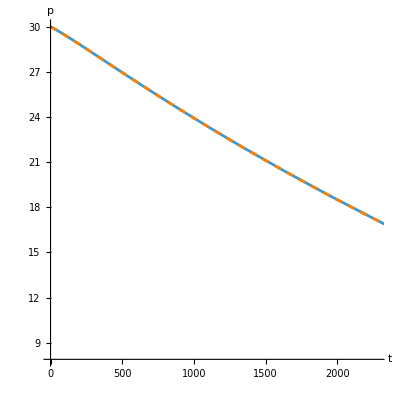

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["p"][χ]}, {χ, 0, plotLimitXi}, AspectRatio->1, AxesLabel->{"t","p"}],ParametricPlot[{t,orbitT["p"][t]}, {t, 0, plotLimitT}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

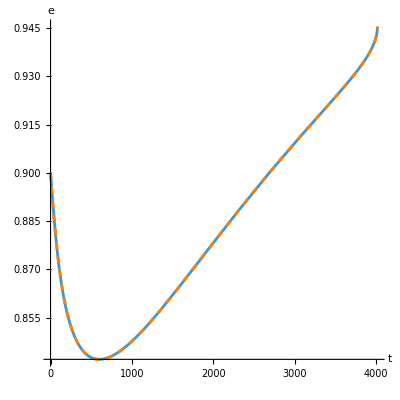

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["e"][χ]}, {χ, 0, plotLimitXi}, AspectRatio->1,AxesLabel->{"t","e"}],ParametricPlot[{t,orbitT["e"][t]}, {t, 0, plotLimitT}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

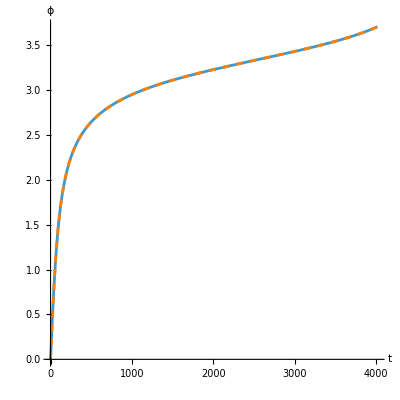

```mathematica
Show[ParametricPlot[{orbit["t"][χ],orbit["ϕ"][χ]}, {χ, 0, plotLimitXi}, AspectRatio->1,AxesLabel->{"t","ϕ"}],ParametricPlot[{t,orbitT["ϕ"][t]}, {t, 0, plotLimitT}, AspectRatio->1,PlotStyle->{Dashed,Orange}]]
```

```mathematica
?Disk
```

Comparison between unperturbed orbit and perturbed

```mathematica
phi[χ_]:=NIntegrate[p0^(1/2)/Sqrt[p0-6-2 e0 Cos[xi+ξ0]],{xi,0,χ}]
```

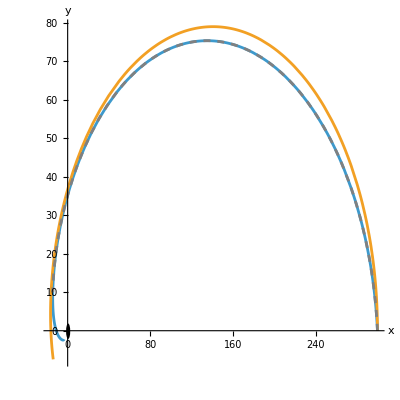

```mathematica
Show[{ParametricPlot[{{orbit["r"][χ]Cos[orbit["ϕ"][χ]], orbit["r"][χ]Sin[orbit["ϕ"][χ]]},{p0/(1+e0 Cos[χ+ξ0]) Cos[phi[χ]], p0/(1+e0 Cos[χ+ξ0])Sin[phi[χ]]}}, {χ,0, plotLimitXi}, AspectRatio->1,PlotRange->All,AxesLabel->{"x","y"}],Graphics[Disk[{0,0},2]],ParametricPlot[{{orbitT["r"][t]Cos[orbitT["ϕ"][t]], orbitT["r"][t]Sin[orbitT["ϕ"][t]]}}, {t,0, plotLimitT/10}, AspectRatio->1,PlotRange->All,PlotStyle->{Gray,Dashed}]}]
```

### Included Models

#### SchwarzGasDrag

Not specifying a Force option means that SchwarzOsculatingOrbitalElements uses the SchwarzGasDrag model.

```mathematica
?SchwarzGasDrag
```

```mathematica
SchwarzGasDrag[p, e, ξ]
```

<|Fr→-e √((-6+p-2 e Cos[ξ])/(p (-3-e^2+p))) Sin[ξ],Fϕ→-(1+e Cos[ξ])^2/(p √(-3-e^2+p))|>

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10293,θ→OsculatingOrbitalElements`Private`θsol$10293,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

One can also specify this option explicitly.

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzGasDrag]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$10843,θ→OsculatingOrbitalElements`Private`θsol$10843,ϕ→InterpolatingFunction[…],p→InterpolatingFunction[…],e→InterpolatingFunction[…],ξ→InterpolatingFunction[…]|>

#### SchwarzFastGSF

One can also choose to use SchwarzFastGSF model. Note that this model is valid for p <= 12 and e<= 0.2.

```mathematica
?SchwarzFastGSF
```

```mathematica
SchwarzFastGSF[p,e,ξ]
```

```mathematica
SchwarzOsculatingOrbitalElements[η, p0, e0, ξ0, Force -> SchwarzFastGSF]
```

Starting NDSolve...

Unbound orbit encountered.

<|t→InterpolatingFunction[{{0., 474691.}}, <>],r→OsculatingOrbitalElements`Private`rsol$12936,θ→OsculatingOrbitalElements`Private`θsol$12936,ϕ→InterpolatingFunction[{{0., 474691.}}, <>],p→InterpolatingFunction[{{0., 474691.}}, <>],e→InterpolatingFunction[{{0., 474691.}}, <>],ξ→InterpolatingFunction[{{0., 474691.}}, <>]|>

## Kerr Spacetime

### Information

#### Method and Notation

This code used the method of Osculating Orbital Elements for Kerr first derived in Gair et al [3] and uses the notation given in that paper.
η is the ratio of the compact object mass to the background black hole’s mass.
p is the semi-lattice rectum.
e is the eccentricity.
x is Cos[θinc].
En is orbital energy.
L angular momentum about the symmetry axis.
K is the modified Carter Constant defined by K = Q + (L - a (En))^2
ψr is the radial phase variable.
ψθ is the polar phase variable.
The equations are integrated w.r.t Mino time λ.
at, ar, aθ, aϕ are covariant components of the acceleration.
ft, fr, fθ, fϕ are vector components of the acceleration.

#### KerrOsculatingOrbitalElements

```mathematica
?KerrOsculatingOrbitalElements
```

```mathematica
?GenericKerrpexBL
```

KerrOsculatingOrbitalElements has the following options.

```mathematica
?Force
```

```mathematica
?IntegrationLimit
```

```mathematica
?AccuracyGoal
```

```mathematica
?PrecisionGoal
```

```mathematica
? TimeMonitor
```

### User Specified Model

First, we are going to define force components for use with KerrOsculatingOrbitalElements. These components need to be functions of En, L, K, ψr and ψθ. We’re just going to use the KerrGasDrag model for this example

Force in covariant form

```mathematica
at[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["at"];
ar[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["ar"];
aθ[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aθ"];
aϕ[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDrag[a, En, L, K, ψr, ψθ]["aϕ"];
```

or in vector form

```mathematica
fr[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fr"];
fθ[ a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fθ"];
fϕ[a_, En_, L_, K_, ψr_, ψθ_] := KerrGasDragVec[a, En, L, K, ψr, ψθ]["fϕ"];
```

Next, we specify the mass ratio, the spin and the initial conditions of the orbit.

```mathematica
η = 10^-3;
a0 = 0.3;
p0 = 40;
e0 = 0.5;
x0 = Cos[π/6];
ψr0 = 0;
ψθ0 =0;
```

Now we solve the osculating geodesic equations and save the result to the symbols ‘ELK’, ‘pex’ and  for different types of parametrisation

Comparison between ELK and pex

```mathematica
(ELK = KerrOsculatingOrbitalElements[η,a0, p0, e0, x0, ψr0, ψθ0, Force -> {at,ar,aθ,aϕ},Parametrisation->"CoordinateTime", TimeMonitor->False]);
AbsoluteTiming[pex = GenericKerrpexBL[η,a0,p0,e0,x0,ψr0, ψθ0,Parametrisation->"CoordinateTime"]];
```

Starting NDSolve...

Separatrix reached.

Starting NDSolve...

Separatrix reached.

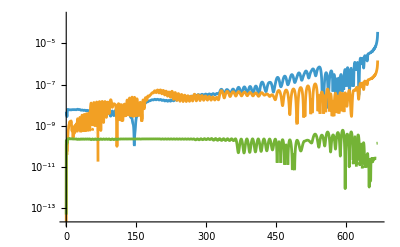

```mathematica
LogPlot[{Abs[pex["p"][t]- ELK["p"][t]],{Abs[pex["e"][t]- ELK["e"][t]]},{Abs[pex["x"][t]- ELK["x"][t]]}},{t,0,ELK["limit"]}]
```

KerrOsculatingOrbitalElements has several options as example ForceUpDown -> "Up" mean that force components are vectors (only fr, fθ, fϕ)

```mathematica
ELKupMino=KerrOsculatingOrbitalElements[η,a0,p0,e0,x0,ψr0,ψθ0,Force->KerrGasDragVec,ForceUpDown->"Up",Parametrisation->"Mino"]
```

Starting NDSolve...

Separatrix reached.

<|t→InterpolatingFunction[…],r→OsculatingOrbitalElements`Private`rsol$1627666,θ→OsculatingOrbitalElements`Private`θsol$1627666,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$1627666,p→OsculatingOrbitalElements`Private`psol$1627666,e→OsculatingOrbitalElements`Private`esol$1627666,x→OsculatingOrbitalElements`Private`xsol$1627666,ι→OsculatingOrbitalElements`Private`ιsol$1627666,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$1627666,r2→OsculatingOrbitalElements`Private`r2sol$1627666,z1→OsculatingOrbitalElements`Private`zmsol$1627666,limit→0.94578|>

comparison with previous ones

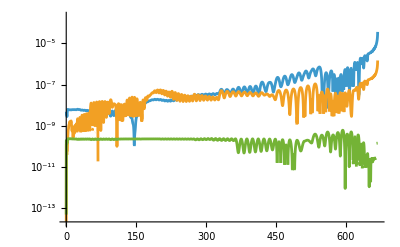

```mathematica
LogPlot[{Abs[pex["p"][t]- ELKup["p"][t]],{Abs[pex["e"][t]- ELKup["e"][t]]},{Abs[pex["x"][t]- ELKup["x"][t]]}},{t,0,ELK["limit"]}]
```

The output is an association . You can access these functions using the following syntax :

```mathematica
pex["r"][100]
```

28.717

```mathematica
ELK["p"][5]
```

39.6122

To find the limit so that we can plot the whole trajectory

```mathematica
plotLimitpex = pex["p"]["Domain"][[1,2]]
plotLimitELKMino = ELKupMino["En"]["Domain"][[1,2]]
```

668.371

0.94578

Plots of different parameters for both parametrisations

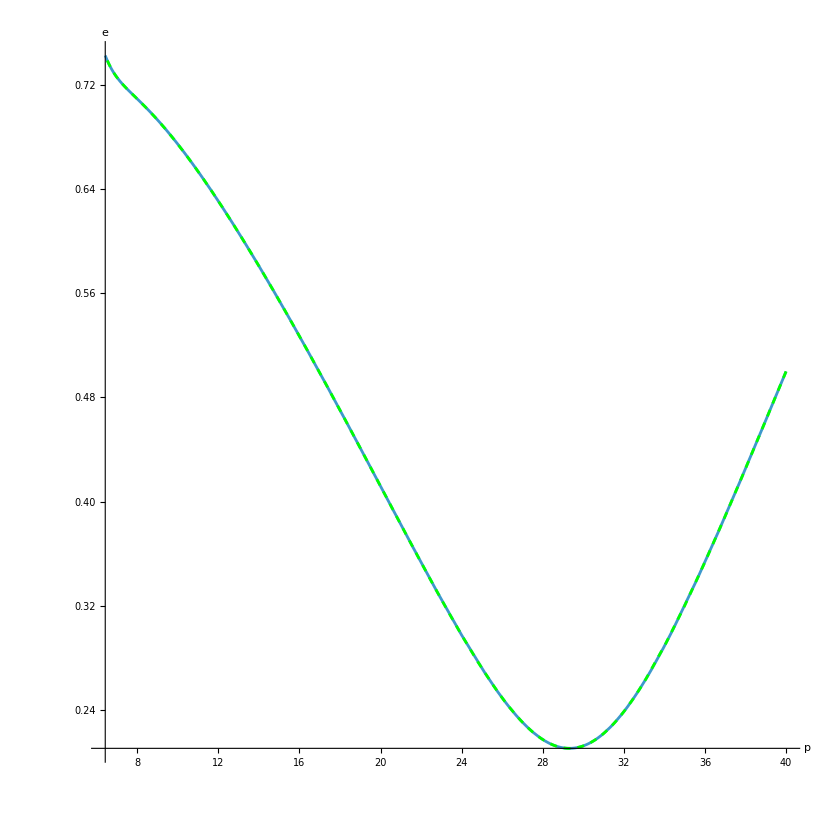

```mathematica
Show[ParametricPlot[{ELKupMino["p"][χ], ELKupMino["e"][χ]}, {χ, 0, plotLimitELKMino}, AspectRatio->1, AxesLabel->{"p","e"}],ParametricPlot[{pex["p"][t], pex["e"][t]}, {t, 0, plotLimitpex}, AspectRatio->1,PlotStyle->{Green,Dashed}] ]
```

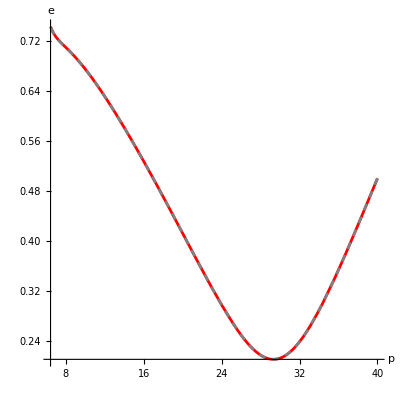

```mathematica
Show[ParametricPlot[{ELKupMino["p"][t], ELKupMino["e"][t]}, {t, 0, plotLimitELKMino}, AspectRatio->1,AxesLabel->{"p","e"},PlotStyle->{Red}],ParametricPlot[{pex["p"][t], pex["e"][t]}, {t, 0, plotLimitpex}, AspectRatio->1,PlotStyle->{Gray,Dashed}]]
```

```mathematica
Show[ParametricPlot3D[{{pex["r"][χ]Cos[ pex["θ"][χ]]Sin[ pex["ϕ"][χ]],pex["r"][χ]Cos[ pex["θ"][χ]]Cos[ pex["ϕ"][χ]],pex["r"][χ]Sin[ pex["θ"][χ]]}}, {χ,0, plotLimitpex},AxesLabel->{"x","y","z"} ,AspectRatio->1]]
```

-Graphics3D-

## References

[1] arxiv.org/abs/0708.3033
[2] arxiv.org/abs/1111.6908
[3] arxiv.org/abs/1012.5111